```mathematica
<<OrbitalMotion`
```

```mathematica
<<RigidbodyKinematics`
```

## Trans & Rot, no RW, no Thrusters

```mathematica
a = 10000;
e = 0.01;
inc = 33.3 Degree;
AN = 48.2 Degree;
AP = -12.2 Degree;
f0 = 85.3 Degree;
```

```mathematica
μ = 0.3986004415 10^6
```

398600.

```mathematica
req = 0.6378136300 10^04
```

6378.14

```mathematica
{rVec0,vVec0} = elem2rv[μ,a,e,inc,AN,AP,f0]
```

(-4020.34 | 7490.57 | 5248.3
-5.19978 | -3.43668 | 1.04158)

```mathematica
{rVec0,vVec0}1000 (* convert to meters *)
```

(-4.02034×10^6 | 7.49057×10^6 | 5.2483×10^6
-5199.78 | -3436.68 | 1041.58)

```mathematica
M0 = E2M[f2E[f0,e],e]
```

1.46885

```mathematica
T = 10.*60
```

600.

```mathematica
ft = E2f[M2E[M0+Sqrt[μ/Abs[a]^3]T,e],e]
```

1.86683

```mathematica
{rVect,vVect}=elem2rv[μ,a,e,inc,AN,AP,ft]
```

(-6781.6 | 4946.87 | 5486.74
-3.89685 | -4.93817 | -0.253846)

```mathematica
{rVect,vVect}1000
```

(-6.7816×10^6 | 4.94687×10^6 | 5.48674×10^6
-3896.85 | -4938.17 | -253.846)

```mathematica
σBN = {0.1,0.2,-.3};
ωBN = {0.001,-0.01,0.03};
Inertia = DiagonalMatrix[{900.,800.,600}];
L = {0,0,0};
```

```mathematica
ans=NDSolve[{
σ'[t]==0.25 BmatMRP[σ[t]].ω[t],
Inertia.ω'[t]==-tilde[ω[t]].Inertia.ω[t]+L, 
σ[0]==σBN,
ω[0]==ωBN
},{σ,ω},{t,0,T}]
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

{{σ→InterpolatingFunction[{{0., 600.}}, <>],ω→InterpolatingFunction[{{0., 600.}}, <>]}}

```mathematica
MatrixForm[{σ[T],ω[T]}/.ans]
```

((-1.63193
-0.479066
3.08557) | (0.00708918
-0.00410849
0.0306095))

```mathematica
-σ[T]/(σ[T].σ[T]) /. ans
```

(0.131465 | 0.0385925 | -0.248567)

```mathematica
σ[T]/.ans
```

(-1.63193 | -0.479066 | 3.08557)

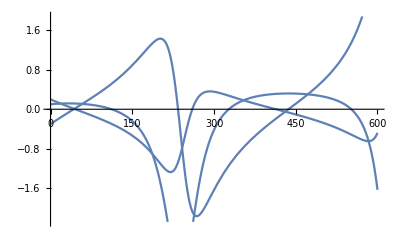

```mathematica
Plot[Evaluate[σ[t]/.ans[[1]]],{t,0,T}]
```

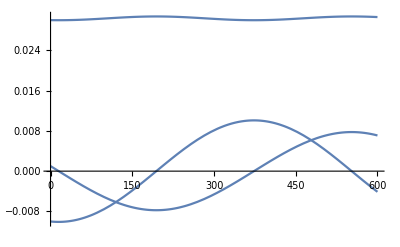

```mathematica
Plot[Evaluate[ω[t]/.ans[[1]]],{t,0,T}]
```